Usando Mathematica.

1. Comando básicos en Mathematica.

```mathematica
1.1  Uso de parentesis.
```

En Mathematica se usan, al igual que muchos otros lenguajes los parentesis "[]", "{}" y "()"; los cuales tiene propositos distintos dependiendo de lo que estemos trabajando.

[ ] 	Se utilizan en los comandos y funciones propias del programa.

Ejemplos :

```mathematica
Cos[π]
```

( ) 	Se utilizan en las expresiones aritmeticas y/o algebraicas que se involucran en las funciones propias del programa.

Ejemplos :

```mathematica
Cos[3(π+π/2)]
```

{ } 	Se utilizan en listas -que veremos posteriormente- y en la separación de las distintas propiedades que posean una función del programa.

Ejemplos :

```mathematica
{1,2}
```

```mathematica
Plot[x^3,{x,-1,1}]
```

1.2 Uso de las comillas " "

Las comillas se utilizan para la aparición de texto ya sea en lo que escribimos en pantalla o bien en un grafico. Mas adelante - en la seccción de graficas - utilizaremos ampliamente las comillas.

Ejemplos

```mathematica
"cosa"
```

1.3 Uso del *

El * posee dos funciones básicas:

Sirve como el operador multiplicación.

Ejemplos :

```mathematica
2*5
```

Nos da la posibilidad de colocar texto en la pantalla de trabajo y que no va a ser tomado en cuenta por el programa. Para hacer esto se debe escribir (*comentario*)

Ejemplos :

```mathematica
2+5 (*calcula la suma de los valores 2 y 5*)
```

1.4 Uso del %

El % nos permite llamar al  (a los) ultimo (s) resultados que el programa nos emitio. Más propiamente el % se refiere a la salida inmediata anterior; %% a la penultima;  %%% a la antepenultima y así sucesivamente.

```mathematica
Ejemplos:
```

```mathematica
Cos[π]
```

```mathematica
Cos[%]
Cos[%]
Cos[%]
Cos[%]
Cos[%]
Cos[%]
Cos[%]
```

```mathematica
Sin[π]
```

```mathematica
Sin[%]
Sin[%]
Sin[%]
Sin[%]
Sin[%]
Sin[%]
```

```mathematica
1.5 Uso del ;
```

Se utiliza para separar instrucciones en una misma línea.

```mathematica
2*3;2+3
```

```mathematica
2*3
```

```mathematica
2*3;
```

Entre las carateristicas tipograficas basicas que podemos encontrar en Mathematica tenemos:

En Matematica se pueden utilizar casi todas las letras del abecedario; así como sus combinaciones.

Matematica difiere las mayusculas de las minusculas.

Los comandos en Matematica se escriben con la primera letra en mayuscula y el resto en minuscula.

Se puede utilizar cualquier letra en minuscula para poder definir o nombrar una cantidad o una variable.

La única letra en mayuscula que se encuentra reservada en Matematica es la letra "E" pues al escribirla estamos haciendo referencia al número neperiano ⅇ; más sin embargo si podemos definir variables o valores formados por mas de una letra entre las cuales se encuentre la letra E.

Ejemplos :

```mathematica
E
```

```mathematica
Pi
```

```mathematica
a
```

```mathematica
A
```

```mathematica
Estrofa
```

1.6 Preguntando a Mathematica.

Muchas veces los comandos o caracteristicas de estos se nos olvidan ... .. para estos casos existen dos soluciones :

Ir a la "ayuda" de Mathematica para ello vamos a la opción "Help" del menu ubicada al final de la barra superior de esta pantalla.

Utilizar los comandos:
			"? Expresion" nos brinda la información basica del comando "Expresión".
			"?? Expresion" nos brinda información más detallada del comando "Expresión".
			"? Expresion*"  nos brinda información de todos los comandos que empiezan con "Expresión".
			"*Expresion*" nos brinda información de todos los comandos que contienen  "Expresión".

Ejemplos:

```mathematica
? Plot
```

```mathematica
?? Plot
```

```mathematica
? Plot*
```

```mathematica
? *Plot*
```

2.Calculos básicos en Mathematica.

2.1 Aritmetica.

Matemática  posee gran capacidad de cálculo arimético; para el cual no se necesita de mucho cuidado en la escritura salvo el de la utilización de los parentesis cuadrados ..... despúes de esto la escritura artimetica se hace de la misma manera que en una calculadora cientifica o algún equivalente a esta.

2.1.1. De las operaciones básicas.

+	Suma dos números o expresiones que escribamos.

-	Resta dos números o expresiones que escribamos.

*	Multiplicación dos números o expresiones que escribamos.

/ 	División dos números o expresiones que escribamos.

^	Exponenciación dos números o expresiones que escribamos.

Ejemplos :

```mathematica
2+3 
2-3
2*3
2/3
2^3
```

2.1.2. Sobre la aproximación de los resultados.

En el apartado anterior vimos que al escribir la expresión 2/3 Mathematica nos da como resultado la fracción 2/3; para poder obtener el valor decimal de esta y otras expresiones debemos de utilizar el comando "N[]".

```mathematica
N[2/3]
```

```mathematica
N[√2]
```

Mathematica por defecto presenta 6 decimales de aproximación y de los cuales aveces redondea el último. Otra forma de obtener expresiones decimales consiste en la utilización de un punto decimal "." en los números. Esto hace que Mathematica asuma que los valores utilizados son decimales y, en consecuencia, devuelva valores decimales.

```mathematica
2./3
```

```mathematica
2/3.
```

Tambien podemos determinar el número de decimales con los cuales aparecera nuestro resultado; esto se hace con el comando N[expr, n] en donde "n" representa el número de digitos que se nos imprimira en pantalla.

```mathematica
N[√2,1] 
N[√2,2]
N[√2,5]
N[√2,10]
N[√2,15]
N[√2,20]
```

```mathematica
N[√3 + Log[5],2000]
```

La única limitante del comando anterior es que -en algunos casos- "n" no puede sobrepasar la capacidad de la maquina en la que trabajamos. Para determinar la capacidad de la misma utilizamos el comando "$MachinePrecision" y con el comando "Presicion " podemos saber la precision con la cual Mathematica calculará un resultado.

```mathematica
$MachinePrecision
```

```mathematica
Precision[√2.]
```

```mathematica
Operaciones boleanas
```

2.1.3 Operadores de Comparación

>,   <		Mayor y menor que. 
>=,  <=		Mayor o igual y Menor o igual.
  = =		Comparación de igualdad.

Ejemplos :

```mathematica
5≤ 8
x>2
{1,2} == {2,1}
```

2.1.4 Operadores Logicos

False		Asignado como valor de falsedad.
True		Asignado como valor de verdad.
&&  		Es la disyunción lógica "y"
||		Es la conjunción lógica "o"

```mathematica
7>22
5≥-3
(2>0)||(6<14)
(-3>7)&&(3>4)
√2.<17/12
```

2.1.5 Variables y Constantes

Para asignar un valor a una letra simplemente escribimos " letra = valor " esto nos permite utilizar la misma posteriormente

```mathematica
a=3
```

```mathematica
a+2
```

igual podemos preguntarle a matematicas por el valor de alguna letra que hayamos usado

```mathematica
?a
```

Lo que siempre debemos de tener presente es el valor asignado a la variable dada; en caso que deseemos cambiar el valor de una variable que hayamos usado podemos utilizar el siguiente comando

```mathematica
Clear[a]
```

Expresiones diferidas
estas espresiones se definen cone l comando ":=" el cual es distinto del comando de asignacion "=".
Por ejemplo el comando "Random[]" nos da un numero aleatorio entre 0 y 1; el cual salvo una casualidad será distinto cada vez que ejecutemos el comandon Random[]

```mathematica
Random[]
Random[]
Random[]
```

ahora bien si usamos el asigandor "=" vamos a asignar el valor que deseemos a la expresion que citemos; por ejemplo

```mathematica
k=Random[]
```

cada vez que usemos el valor "k" este va a tener asignado el valor que acabamos de obterner

```mathematica
k+1
```

si por el contrario utilizamos el comando de asignacion inmediata ":=" el valor de k puede ir variando cada vez que lo ejecutemos

```mathematica
k:= Random[]
```

en este caso estamos asignando un valor aleatorio a la letra "k" ; sin embargo no obtenemos nada como salida pues no hemos preguntado por el valor de "k" ni tampoco lo hemos utilizado en ninguna expesión.

```mathematica
k
k
k
```

```mathematica
Resolviendo Ecuaciones:
```

```mathematica
Roots[4((3x)/4-1/2)-1/2(4x+12)==4,x]
```

```mathematica
Solve[a/(2 y)+y^2==x+(y a)/(2x),a]
```

```mathematica
Solve[10 x^2+59 x+62==0,x] //N
```

```mathematica
NSolve[10 x^2+59 x+62==0,x]
```

```mathematica
N[%%]
```

```mathematica
Solve[8h^(-6)-65 h^-3+8==0,h]
```

```mathematica
Reduce[√(a^2+4a+1)-√(2a+4)==0,a]
```

```mathematica
Solve[√x+√(1+x)-√(2+x)==√(k+x),x]
```

```mathematica
Solve[{16h-11b+17==11h+6b+17,9h-9b+21==-14h+8b-23},{h,b}]
```

```mathematica
Reduce[(x^2-4)(x^2-4x+4)(x^2-6x+8)(x^2+4x+4)<0,x]
```

```mathematica
Reduce[Abs[t+3]<4 ,t, Reals ]
```

```mathematica
Reduce[Abs[(a^2-3 a-1)/(a^2+a+1)]≤3,a, Reals]
```

```mathematica
Reduce[12 x^5+56 x^4-11 x^3-252 x^2-127 x+70<0 ,x]
```

2.1 .5 .1. Comandos Simplify y Expand.

```mathematica
Comando Simplify
```

*Este comando nos ayuda a la simplificación de expresiones; no importa si las mismas son o no expresiones algebraicas.
*Es importante recordar que en este comando - así como en muchos otros - la primera letra del comando - en este caso la "s" - se escribe en mayuscula y dentro de los parentesis que deben de ser cuadrados [ ] escribimos la expresión que deseamos simplificar.
*Un error muy común consiste en el uso de paréntesis cuadrados dentro de una expresión.

Ejemplos :

```mathematica
Simplify[x^3+10 x y-5 x y+3 x+10 √x+2 √x+4 y+y]
```

```mathematica
Simplify[(6 x^2-10)/2+(6 x^2-6x+12)/-6-(8 x^2+12 x-20)/4]
```

```mathematica
Simplify[((a+b-c)-(a-b+c))-((b-c+a)-(b+c-a))]
```

```mathematica
Simplify[∫xⅆx - ∫x^2 ⅆy]
```

```mathematica
Comando Expand
```

*Al contrario que el comando Simplify el comando Exapand comando nos ayuda a la expansión de expresiones; no importa si las mismas son o no expresiones algebraicas.
*Es importante recordar que en este comando - así como en muchos otros - la primera letra del comando - en este caso la "s" - se escribe el mayuscula y dentro de los parentesis que deben de ser cuadrados[] escribimos la expresión que deseamos simplificar

Ejemplos

```mathematica
Expand[(3 x^2 y z-4 x y^2 z^3)(2 x y^2 z^4)]
```

```mathematica
Expand[(a^4+a^3+a b^2+b^2)(-a^4+a^3+a b^2-b^2)]
```

```mathematica
Expand[(8 p^3 q^4 r^5)(4 p^2 q^3-3 q^5 r^6)-(4 p^3 q^7 r^4)(-3 p^3 q+8 p^2 r-6 q^2 r^7)]
```

```mathematica
Expand[(1-x)^10]
```

```mathematica
Comando Apart
```

Este comando nos ayuda a calcular la descomposición  en fracciones parciales de una expresión.

Ejemplos

```mathematica
Apart[(6 x^3+3 x^2-24 x-9)/(2 x-3)]
```

2.2. Funciones.

Para definir la función "f(x)=expresion" lo primero que tenemos que hacer es decirle a Matemática que la letra "x" es una variable lo cual se hace escribiendo "x_". Entonces para escribir la funcion "f(x)= x^5" podemos escribir

```mathematica
f[x_]= x^5
```

o  bien

```mathematica
j[x_]:= x^5
```

pudiendo ahora calcular cualquier expresion que deseemos en la función f (x)

```mathematica
f[2]
f[y]
f[casa]
```

Tambien podemos definir funciones de varias variables de la siguiente forma :

```mathematica
g[x_,y_]=x+5y
```

```mathematica
h[x_]:= N[x,30]
h[Pi]
```

```mathematica
j[x_]= N[x,30]
```

```mathematica
j[Pi]
```

¿Cuál es la diferencia de definir una función utilizando el asignador "=" o bien el asignador ":="? (como se acaba de hacer)

Está claro lo que ha pasado. Al definir f[x] con la asignación inmediata se evalúa enseguida el comando N[x, 30] y, como x no es una cantidad numérica, Mathematica da como respuesta el propio x que es lo que de aquí en adelante Mathematica interpretará como f["deloquesea"]. Ahora hemos definido f[x] con la asignación diferida por lo que el comando N[x, 30] no se evalúa hasta que se llama a la función.

¿Cuál es la diferencia de las siguientes expresiones?

```mathematica
Clear[f,g]
f[x_]=Simplify[x];
g[x_]:=Simplify[x];
f[Cos[x]^2+Sin[x]^2]
g[Cos[x]^2+Sin[x]^2]
```

```mathematica
Definiendo funciones a trozos
```

```mathematica
H[x_ /; x >0]=x;
H[x_ /; x ≤ 0] = x^3;
```

```mathematica
{H[1], H[-4]}
```

```mathematica
Polinomios
```

Mathematica nos permite definir polinomios de una y varias variables  por medio de la definición de funciones - recordemos que al fin y al cabo un polinomio se puede visualizar con una función de una o varias variables según sea el caso -; asi mismo existen varios comandos que se pueden utilizar para el trabajo con polinomios; varios de estos son:

```mathematica
ClearAll[f,g]
 f[x_]=2 x^2; g[x_]=x^2-5x+6;
{Suma[x_]=Simplify[f[x]+g[x]], Resta[x_]=Simplify[f[x]-g[x]],Producto[x_]=Simplify[f[x]*g[x]],Divi[x_]=Simplify[f[x]/g[x]],Composition[f,g][x],f[g[x]], Composition[g, f][x],g[f[x]]}
```

```mathematica
P[x_] :=(1-x)^1000;
```

```mathematica
Coefficient
```

```mathematica
Coefficient[P[x],x,1000]
```

```mathematica
PolynomialGCD
```

```mathematica
PolynomialGCD[P[x],6 x^3+3 x^2-24 x-9]
```

```mathematica
PolynomialLCM
```

```mathematica
PolynomialLCM[P[x],6 x^3+3 x^2-24 x-9]
```

```mathematica
Exponent
```

Nos da el grado del polinomio con respecto a la variable z.

```mathematica
Exponent[poli2,z]
```

```mathematica
Together
```

Nos da el mismo resultado que el comando Simplify

Ejemplos :

```mathematica
Together[(2-(a+5)/(a+2))/(a^2-1)+(a^2-(3 a^2-a)/(a+2))/(a^3+1)]
```

```mathematica
Together[b/(b^2-b-2)-1/(b^2+5 b-14)-2/(b^2+8 b+7)]
```

Ejemplos variados :

```mathematica
H[x_]:=Tan[x]Abs[√x];
PolynomialQ[H[x],x]
```

```mathematica
PolynomialQuotient[6 x^3+3 x^2-24 x-9,2x-3,x]
```

```mathematica
PolynomialRemainder[6 x^3+3 x^2-24 x-9,2x-3,x]
```

```mathematica
Factor[x(a+b+c)-y(a+b+c)]
Factor[-3 d p+6 d q+3 d x+p^2-2 p q-p x]
Factor[12 x^(2 m)-7 x^m-12]
Factor[4 b^2 x+4 b x^2-4 b x+x^3-2 x^2]
```

```mathematica
Simplify[(2 d^2-d v-v^2)/(4 d^2-4 d v+v^2)*(8 d^2+6 d v-9 v^2)/(4 d^2-9 v^2)]
Factor[%]
```

```mathematica
Simplify[(a^2-b^2)/(2 a^2-3 a b+b^2)*(2 a^2+5a b-3 b^2)/(a^2+4a b+3 b^2)*(a^2-2 a b-3 b^2)/(a^2-4 a b+3 b^2)]
```

```mathematica
FullSimplify[1+(1+(1+(1+(1+1/x)/x)/x)/x)/x /. x->1+y^2]
```

```mathematica
A[r_]=(2 r-1)/(r^2+2 r-3);{A[3], A[1/2], A[-1], Simplify[A[x^2+1]]}(* Se ha generado una lista. El ; se utiliza para separar instrucciones en una misma línea *)
```

```mathematica
Graficando en Mathematica.
```

```mathematica
Puntos:
```

```mathematica
ListPlot[{{2,3}},PlotStyle -> PointSize[0.025]]
```

```mathematica
ListPlot[{{0,-1},{1,2},{2,4}}, PlotStyle -> PointSize[0.025]] (* Variar el valor de PointSize *)
```

```mathematica
Funciones
```

```mathematica
Plot[Sin[x],{x,-3Pi, Pi}]
```

```mathematica
Plot[E^x, {x,-3,3}]
```

```mathematica
Plot[1/(x+1), {x,-3,3}]
```

```mathematica
Plot[{x/(x^2+1),x^2},{x,-4,4}, PlotRange->{-1,4}]
```

```mathematica
Plot[1,{x,-1,5}]
Plot[1,{x,-1,5},PlotRange->{-1,4}]
```

```mathematica
Gráfica de una función definida a trozos
```

```mathematica
g[x_ /; x ≤ 0]=x^2;
g[x_ /; x>0] = Abs[x];
Plot[g[x], {x, -5,5}]
```

```mathematica
Clear[x,y];
y=30-x;
Ppro[x_]=x^2 y^3;
Plot[Ppro[x], {x,0,31}]
Table[{i,Ppro[i]}, {i, 11, 13, 0.1}]
```

```mathematica
Observe que se intuye -grafica y numericamente- que la función posee un máximo en 12
```

```mathematica
Graficando regiones sombreadas
```

```mathematica
Plot[2Sin[x]+x,{x,0,15},Filling->Bottom]
```

```mathematica
Plot[{Sin[x]+x/2,Sin[x]+x}, {x, 0, 10},Filling->{1->{2}}]
```

```mathematica
Table[Plot[Sin[x],{x,0,2Pi},Filling->f],{f,{Axis,Top,Bottom,0.3}}]
```

```mathematica
Table[Plot[Sin[x],{x,0,2Pi},Filling->Axis,FillingStyle->c],{c,{Red,Green,Blue,Yellow}}]
```

```mathematica
Plot[Sin[x],{x,0,2Pi},Mesh->20]
```

```mathematica
Plot[Sin[x],{x,0,2Pi},Mesh->{Range[0,2Pi,Pi/4]},MeshStyle->PointSize[Medium]]
```

```mathematica
Plot[Tan[x],{x,0,Pi/2},Mesh->{5,10},MeshFunctions->{#1&,#2&},MeshStyle->{Directive[PointSize[Medium],Red],Blue}]
```

```mathematica
Table[Plot[Sin[x],{x,0,2Pi},PlotPoints->i,MaxRecursion->0],{i,{5,10,15,25}}]
```

```mathematica
Plot[1/x,{x,-2,2},Frame->True]
```

```mathematica
Table[Plot[Sin[x],{x,0,2Pi},PlotStyle->ps],{ps,{Red,Thick,Dashed,Directive[Red,Thick]}}]
```

```mathematica
Plot[Sin[x],{x,0,8Pi},RegionFunction->Function[{x,y},Abs[y]>0.5]]
```

```mathematica
Plot[Sin[x],{x,0,8Pi},RegionFunction->Function[{x,y},Pi/2<Mod[x,2Pi]<3Pi/2]]
```

```mathematica
Plot[{Exp[x],Log[x],x},{x,-3,3},PlotRange->3,PlotStyle->{Red,Green,Dashed}, AspectRatio->Automatic]
```

```mathematica
Programando en Mathematica.
```

```mathematica
Algunos ejercicios básicos
```

```mathematica
Calculemos la distancia entre dos puntos:
```

```mathematica
distancia[x1_,y1_,x2_, y2_]:=√((x2-x1)^2+(y2-y1)^2);
distancia[0,-1, 2, 4]
```

```mathematica
Calculemos el punto medio de un segmento de recta
```

```mathematica
PM[x1_,y1_,x2_,y2_]:={(x1+x2)/2,(y1+y2)/2};
PM[1, 2, 2, 4]
```

```mathematica
Calculemos el area de un triángulo sabiendo sus lados.
```

```mathematica
semip[x_,y_,z_]=(x+y+z)/2;
s=semip[distancia[x1,y1,x2,y2],distancia[x1,y1,x3,y3],distancia[x2,y2,x3,y3]];
Area[x1_,y1_,x2_,y2_,x3_,y3_]=√(s(s-distancia[x1,y1,x2,y2])(s-distancia[x1,y1,x3,y3])(s-distancia[x2,y2,x3,y3]));
N[Area[5,-1,2,5,-1,-4]]
```

```mathematica
Determinemos la recta que pasa por los puntos (a,b) y (c,d)
```

```mathematica
pen[x1_,y1_,x2_,y2_]:=(y2-y1)/(x2-x1);
b[x1_,y1_,x2_,y2_]:=y1-pen[x1,y1,x2,y2]*x1;
y[x1_,y1_,x2_,y2_] := pen[x1,y1,x2,y2] *x +b[x1,y1,x2,y2]
```

```mathematica
y[1,2,0,1]
```

```mathematica
Recurrencia.
```

```mathematica
ClearAll[F];
F[n_]:=F[n-1]+F[n-2];
F[0]=1;
F[1]=1;
(* Cuando se crea una recursión se coloca := *)
Table[{i, F[i]},{i, 0, 10, 1}]
```

```mathematica
Solicitando datos al usuario
```

```mathematica
a=Input["a"];
b=Input["b"];
proAB  = a * b;
Print[proAB];
```

```mathematica
cap=Input["¿Cuál es el capital?"];
ganancia=cap * 0.02;
Print[ganancia];
```

```mathematica
suelB=Input["Digite el sueldo base"];
venta1=Input["Digite el valor de la primera venta"];
venta2=Input["Digite el valor de la segunda venta"];
venta3=Input["Digite el valor de la tercera venta"];
totalventa=venta1+venta2+venta3;
comision=totalventa*0.10;
sueldoR=suelB+comision;
Print[sueldoR,comision];
```

```mathematica
Usemos el IF
```

```mathematica
El patron para utilzar este comando es IF[Condición, valor en caso de que sea cierta, valor en caso de que sea falsa]
```

```mathematica
El punto (a,b) esta en la recta y=mx+b ??
```

```mathematica
y[x_] := 3x-6
```

```mathematica
If[y[1] == -3,"True","False"]
```

```mathematica
Determinemos is un número es o no positivo
```

```mathematica
Positivo[num_]:= If[num≥0, Print["Verdadero"], Print["Falso"]];
```

```mathematica
Positivo[-5]
```

```mathematica
Intersección de una recta con el eje x
```

```mathematica
solun[a_,b_]:=If[a!=0, Print[-b/a], If[b == 0, Print["La solución es R"], Print["La solución en vacía"]]];
```

```mathematica
solun[1,2]
```

```mathematica
Clasificación de un triángulo según la medida de sus lados
```

```mathematica
TipoTrian[a_,b_,c_]:=If [a==b&&b==c, Print["Equilátero"],If [a==b||b==c||c==a,
Print["Isósceles"], Print["Escaleno"]];]
```

```mathematica
TipoTrian[1,2,3]
```

```mathematica
Ordenemos el orden de tres números
```

```mathematica
EncuentraMayor[ a_, b_, c_]:= If [a > b, If [a > c, Print[a],Print [c] ], If [b > c, Print[b],
 	     Print[c]]]
```

```mathematica
EncuentraMayor[656,10000,1300]
```

```mathematica
Este año es bisiesto??
```

```mathematica
bisiesto[ a_]:=If [Mod[a,4]==0&&Mod[a , 100]!=0, v=True,If [Mod[a , 100]==0 &&Mod[a,400]==0, v= True,v= False]]
diasMes[mes_, a_]:= Switch [mes,4  , Print[30],6 ,Print[30],9 ,Print[30],11,Print[30],2, If[bisiesto[a]==True, Print[29], Print[28]], 1, Print[31], 3, Print[31], 5, Print[31], 7, Print[31], 8, Print[31], 10, Print[31], 12, Print[31]]
```

```mathematica
diasMes[10,2010]
```

```mathematica
Determinemos si un triángulo es o no rectángulo.
```

```mathematica
Binomial[3,2]
TrRec[x1_,y1_,x2_,y2_,x3_,y3_]:=If[((distancia[x1,y1,x2,y2])^2+(distancia[x2,y2,x3,y3])^2==(distancia[x1,y1,x3,y3])^2) || ((distancia[x1,y1,x3,y3])^2+(distancia[x3,y3,x2,y2])^2==(distancia[x1,y1,x2,y2])^2)|| ((distancia[x2,y2,x3,y3])^2+(distancia[x3,y3,x1,y1])^2==(distancia[x1,y1,x2,y2])^2), Print["True"], Print["False"]]
TrRec[-1,-4,2,5,5,-1]
```

```mathematica
If[y[1]==-3, Print["True"], Print["False"]]
```

```mathematica
Clear[a,bbb,c];
a=Input["Digite el valor de a: "];
bbb=Input["Digite el valor de b: "];
c= Input["Digite el valor de c: "];
Print["f(x)=",a x^2+bbb x+c];
Print["Intersecciones con el eje x"];
If[bbb^2-4 a c≥ 0, Print["Las raíces son:"]; Print["x1= ", N[(-bbb+√(bbb^2-4 a c))/(2 a)], ", x2= ", N[(-bbb-√(bbb^2-4 a c))/(2 a)]], Print["No hay raíces reales"]]
If[a>0,Print["Es Concava hacia arriba"],Print["Es Concava hacia abajo"]]
Print["El vértice es: ", "(", Simplify[-bbb/(2 a)], ",",Simplify[(-(bbb^2-4 a c))/(4 a)],")"]
If[a>0, Print["En este par ocurre un mínimo absoluto"],Print["En este par ocurre un máximo absoluto"] ]
Print["La intersección con el eje y ocurre en: (0," ,c,")"]
t1=Input["Valor menor del intervalo del plot: "];
t2=Input["Valor mayor del intervalo del plot: "];
Plot[a x^2+bbb x+c, {x, t1,t2}]
```

```mathematica
Usemos el For
```

Factorice los polinomios de la forma "x^2-n " en donde "n" es un número natural menor que 11

```mathematica
For[i=1,i≤3,i++,Print[i]]
```

```mathematica
Clear[i]
For[i=1,i≤10,Print[Factor[x^2-i]];i++]
```

```mathematica
While
```

```mathematica
n=1;While[n<4,Print[n];n++]
```

```mathematica
n=1;While[++n<4];n
```

```mathematica
n=1;While[True,If[n>10,Break[]];n++]
```

```mathematica
Factorizando un número
```

```mathematica
While[True,
n=Input["Digite un Entero"];
If[!IntegerQ[n]||n≤0,Break[]];
Print[n,"=",FactorInteger[n]]]
```

```mathematica
con=1;
suma=0;
Prom[ No_]:=While [con<= No, num=Input["Digite el valor"];suma = suma + num; If[con == No,  Print[N[suma/No]]]; con= con +1 ;];
```

```mathematica
Prom[3]
```

```mathematica
Do
```

```mathematica
Do[Print[n^2],{n,4}]
```

```mathematica
Do[Print[n],{n,-3,5,2}]
```

```mathematica
Do[Print[{i,j}],{i,4},{j,i-1}]
```

```mathematica
t=1;Do[t*=k;Print[t];If[t>19,Break[]],{k,10}]
```

```mathematica
t=1;Do[t*=k;Print[t];If[k<2,Continue[]];t+=2,{k,5}]
```

```mathematica
t=x;Do[t=1/(1+t),{5}];t
```

```mathematica
t={};Do[If[PrimeQ[2^n-1],AppendTo[t,n]],{n,100}];t
```

```mathematica
Reap[Do[If[PrimeQ[2^n-1],Sow[n]],{n,100}]]⟦2,1⟧
```

```mathematica
Switch
```

```mathematica
Cal[o1_, o2_, o_]:=Switch[o, "+", Print[o1+o2], "-", Print[o1-o2],"*", Print[o1*o2], "/", Print[o1/o2]]
Cal[4,4,"*"]
```

```mathematica
Ejemplos Varios:
```

```mathematica
ParesEntre[n_,m_]:=If[n<m, num=n; While [num <  m, If[Mod[num ,2] == 0, Print[num]];num = num +1 ;];]
ParesEntre[2,20]
```

```mathematica
Divisores[n_]:=For[i=1, i<=n , i++, If[Mod[n, i] == 0, Print[i];]]
Divisores[10]
```

```mathematica
SumaSerie[ n_]:=For[i = 1, i< n, i++,If[i==1, suma=1; signo=-1;];suma = suma + signo/(2* i);signo=-signo; If[i==n-1, Return[suma]]];
SumaSerie[4]
```

```mathematica
Sumdiv[n_]:=For[j=1,j<=n,j++,If[j==1,suma=0];If[Mod[n,j]==0,suma = suma+j];If[j==n,Return[suma]];]
```

```mathematica
SonAmigos[n_,m_]:=If[Sumdiv[n]==Sumdiv[m], Print["Son amigos"], Print["No son amigos"]];
SonAmigos[284,220]
```

```mathematica
S=0; i=1;
TipNum[ N_] :=While [i<= N/2, If [ Mod[N , i] == 0, S= S + i;] ;i ++;If[i>N/2, If[S>N, Return[2], If[S<N, Return[1], Return[3]]];]] 
TipNum[10]
```

```mathematica
i=2;
Legendr[x_, n_]:=While [i<=n, If[i==2, pn2= 1;  pn1= x;] ; pn = ((2*i-1)/ i) * x * pn1 - (( i-1)/i)* pn2; pn2 = pn1; pn1 = pn;i++;If[i==n, Return[pn];]] 
Legendr[2, 5]
```

```mathematica
PuntosDeCorte[x1_, y1_, r1_,x2_, y2_,r2_]:=If[Sqrt[(x1 - x2)*(x1 - x2) + (y1 - y2)*(y1 - y2)] == 0,If[r1 == r2, Print["Existen infinitos puntos de corte"],Print["No hay puntos de corte"]],If[r1+r2 < Sqrt[(x1 - x2)*(x1 - x2) + (y1 - y2)*(y1 - y2)] ,Print["Existen dos puntos de corte"],If[r1+r2== Sqrt[(x1 - x2)*(x1 - x2) + (y1 - y2)*(y1 - y2)] ,Print["Existe un punto de corte"],Print["No hay puntos de corte"];];];];
PuntosDeCorte[1,1,1,1,1,1]
```

```mathematica
Calculo en Mathematica
```

```mathematica
Derivadas de una función
```

```mathematica
f[x_]=x^2 Sin[x];
Expand[Limit[(f[x+h]-f[x])/h,h->0]]
D[f[x],x]
```

```mathematica
Determinemos la diferenciabilidad de una función en un punto dado.
```

```mathematica
f[x_]=Abs[x-1]+Abs[x+1];
Plot[f[x], {x, -2, 2}, PlotRange -> {-1,5}]
Limit[(f[-1+h]-f[-1])/h,h->0, Direction -> -1] (* A la derecha *)
Limit[(f[-1+h]-f[-1])/h,h->0, Direction -> 1] 
(* A la izquierda *)
Limit[(f[1+h]-f[1])/h,h->0, Direction -> -1] (* A la derecha *)
Limit[(f[1+h]-f[1])/h,h->0, Direction -> 1] 
(* A la izquierda *)
```

```mathematica
Derivadas de orden superior
```

```mathematica
Simplify[D[(1+√(ⅇ^x+1))/(1+x^2), x,x,x]]
```

```mathematica
H.b4opital
```

```mathematica
f[x_]=(Sin[x]-x)/x^3;
While[((Numerator[f[x]] /. x->0)==0) &&((Denominator[f[x]] /. x->0)== 0), f[x_]=Together[D[Numerator[f[x]],x]/D[Denominator[f[x]],x]]; Print[f[x]];]
Print[f[0]]
```

```mathematica
Resolviendo una ecuación diferencial
```

```mathematica
D[x^2+x y[x]+2(y[x])^2==28,x];
% /. y'[x] ->yp;
Solve[% , yp ];
% /. {x ->2,y[x]->3}
```

```mathematica
f[x_]=6x-(7 x^2)/2-12 x^3+(7 x^4)/4+(6 x^5)/5;
v=Solve[D[f[x],x]==0,x]
P={};
For[i=1, i≤Length[v], P=P∪{{x /. v[[i,1]],f[x] /. v[[i,1]]}}; i++]
Print["Los puntos estacionarios son: ",P]
```

```mathematica
Animación de Graficos.
```

```mathematica
Animate[Plot[ x^2+ x+k1, {x,-10,10}, PlotRange->{-5,20}], {k1, 1, 20, 1}, AnimationRunning->False]
```

```mathematica
Animate[Plot[Sin[a x]+Sin[b x],{x,0,10},PlotRange->2],{a,1,5},{b,1,5},AnimationRunning->False]
```

```mathematica
Animate[Nest[Subsuperscript[#,#,#]&,x,n],{n,1,5,1},AnimationRunning->False]
```

```mathematica
Table[Animate[FactorInteger[n],{n,1,2000,1,AppearanceElements->a}],{a,{"ProgressSlider","StepLeftButton","StepRightButton","PlayPauseButton","FasterSlowerButtons","DirectionButton","ResetButton","PlayButton","ResetPlayButton"}}]
```

```mathematica
Table[Animate[Graphics[Disk[{u,0}],PlotRange->{{-1,2},{-1,1}},ImageSize->30],{u,0,1},AnimationRunning->False,Alignment->a],{a,{Left,Center,Right}}]
```

```mathematica
Table[Animate[u,{u,0,1},AnimationRunning->False,AppearanceElements->a],{a,{"HideControlsButton","SnapshotButton","ResetButton","UpdateButton",All}}]
```

```mathematica
Table[Animate[u,{u,0,1},AnimationRunning->False,ControlPlacement->p],{p,{Left,Right,Bottom,Top}}]
```

```mathematica
Table[Animate[u,{u,0,10},DefaultDuration->a,AnimationRunning->False],{a,1,3}]
```

```mathematica
Table[Animate[u,{u,0,1},AnimationDirection->a,AnimationRunning->False],{a,{Forward,Backward,ForwardBackward}}]
```

```mathematica
Table[Animate[Graphics[Disk[{u,0}],PlotRange->{{-1,2},{-1,1}},ImageSize->30],{u,0,1},AnimationRunning->False,Alignment->a],{a,{Left,Center,Right}}]
```

```mathematica
CreateDialog[Animate[f[x],{x,0,1},Initialization:>{f[c_]:=Graphics[{Hue[c],Disk[]},ImageSize->Tiny]},Deinitialization:>CreateDialog[f[x]]]];
```

```mathematica
Animate[Graphics[{Point[{Sin[x],Cos[x]Sin[x]}]},PlotRange->1,ImageSize->Tiny],{x,0,20 Pi,.1},AnimationRunning->False]
```

```mathematica
Table[Animate[Framed@u,{u,0,1},AnimationRunning->False,FrameMargins->f],{f,{Tiny,Small,Medium,Large}}]
```

```mathematica
Animate[Graphics[Translate[Rotate[{Circle[],Point[{0,1}]},-t],{t ,0}],PlotRange->{{-2,10},{-2,2}},ImageSize->{Large,Tiny}],{t,0,2π},AnimationRunning->False]
```

```mathematica
Animate[Column[{Plot[{Sin[f1 x+t],Sin[f2 x-t]},{x,-2 π,2 π},PlotRange->1.1],Plot[Sin[f2 x-t]+Sin[f1 x+t],{x,-2 π,2 π},PlotRange->2]}],{f1,1,10},{f2,1,10},{t,0,2 π},AnimationRunning->False]
```

```mathematica
Animate[Plot[Sin[x+a],{x,0,10},PlotLabel->a],{a,0,Infinity},AnimationRunning->False]
```

```mathematica
Animate[ParametricPlot[Through[{Re,Im}[(x+I y)^s]],{x,-2,2},{y,-2,2},PerformanceGoal->"Quality",PlotLabel->z^s,PlotRange->{{-2,2},{-2,2}}],{s,0,1},AnimationRunning->False]
```

```mathematica
DynamicModule[{x=0,xlis={{0,0}}},{Animator[Dynamic[x,(x=#;AppendTo[xlis,{#,#}])&]],Graphics[Line[Dynamic@xlis],Axes->True,PlotRange->{{0,1},{0,1}}]}]
```

```mathematica
ListAnimate[Table[Graphics[Line[{{0,0},{x,x}}],Axes->True,PlotRange->{{0,1},{0,1}}],{x,0,1,0.01}]]
```

```mathematica
Animate[Graphics[{Circle[],Point[{Cos[t],Sin[t]}]}],{t,0,6},AnimationRunning->False]
```

```mathematica
Animate[Plot[t(x^2-1)+(1-t)(-x^2),{x,-1,1},Axes->False,Epilog->{Circle[{0,1},3],Disk[{1,2},.3],Disk[{-1,2},.3],Line[{{0,0.6},{0,1.6}}]},PlotRange->{{-3,4},{-3,4}},AspectRatio->1],{t,0,1},AnimationRunning->False]
```

```mathematica
Animate[Plot3D[Sin[x+a]Sin[y+b],{x,0,2Pi},{y,0,2Pi},PlotRange->1],{a,0,Pi},{b,0,Pi},AnimationRunning->False]
```

```mathematica
DynamicModule[{n=5,data=Table[RandomReal[],{20}]},
Column[{
Slider[Dynamic[n],{1,20,1}],Dynamic[Column[Table[With[{i=i},Slider[Dynamic[data[[i]]]]],{i,n}]]]}]]
```

```mathematica
Show[Graphics[{Pink,Rectangle[]},DisplayFunction->(PopupWindow[Button["Presione Aquí"],#]&)]]
```

```mathematica
DynamicModule[{x=12},{Slider[Dynamic[x],{10,100}],Style["Hola",FontSize->Dynamic[x]]}]
```

```mathematica
n=1;
Column[{Slider[Dynamic[n],{1,10}],Dynamic[Module[{n1=n},Graphics[Line[Table[{x,Sin[n1 x]},{x,0,2Pi,0.0001}]]]],SynchronousUpdating->False]}]
```

```mathematica
DynamicModule[{n=1},Column[{Slider[Dynamic[n],{1,10}],Dynamic[{n,ControlActive["Activo","Not Activo"]}]}]]
```

```mathematica
ListAnimate[Table[Graphics[Disk[],ImageSize->RandomReal[100]],{50}]]
```

```mathematica
ListAnimate[{Style["\[MathematicaIcon]",Large],"string",Framed[x+y],Graphics[Rectangle[],ImageSize->20]}]
```

```mathematica
ListAnimate[Table[ListLinePlot[Take[steps,i],Mesh->All,PlotRange->{{-1,1.1},{-1,1.1}}],{i,Length[steps]}]]
```

```mathematica
LUAnimate[RandomInteger[10,{20,20}],MatrixPlot[#,FrameTicks->None,ImageSize->100]&]
```

```mathematica
Dynamic[Pause[3];Style["Hello",100],SynchronousUpdating->False]
```

```mathematica
DynamicModule[{n=3},Column[{Slider[Dynamic[n],{3,1000,1}],Dynamic[Graphics[ControlActive[Inset[n,{0,0}],Line[Table[{{0,0},{Cos[t],Sin[t]}},{t,0.,2Pi,2Pi/n}]]],ImageSize->300,PlotRange->1],SynchronousUpdating->Automatic]}]]
```

```mathematica
DynamicModule[{n=1},Column[{Slider[Dynamic[n],{1,10}],Dynamic[n]}]]
```

```mathematica
DynamicModule[{n=5,data=Table[RandomReal[],{20}]},
Column[{
Slider[Dynamic[n],{1,20,1}],
Dynamic[Grid[Table[With[{i=i},
{Slider[Dynamic[data[[i]]]],data[[i]]}],{i,n}]
]]}]]
```

```mathematica
Table[Module[{x=.5},{Slider[Dynamic[x]],Dynamic[x]}],{2}]
```

```mathematica
DynamicModule[{showclock=True},{Checkbox[Dynamic[showclock]],Dynamic[If[showclock,Refresh[DateList[],UpdateInterval->0.05],"No clock"]]}]
```

```mathematica
Animate[{Slider[u^2],Slider[1-Sqrt[u]]},{u,0,1},AnimationRunning->False]
```

```mathematica
Animate[Graphics[{Circle[],Point[{Cos[t],Sin[t]}]}],{t,0,6},AnimationRunning->False]
```

```mathematica
Animate[Plot[t(x^2-1)+(1-t)(-x^2),{x,-1,1},Axes->False,PlotRange->{{-3,4},{-3,4}},AspectRatio->1],{t,0,1},AnimationRunning->False]
```

```mathematica
<<Graphics`ImplicitPlot`;
```

```mathematica
Animate[ImplicitPlot[3x+ 2y== n,{x,0,5} ,{y,0,5},PlotRange->{0,4}],{n,0,10},AnimationRunning->False];
```

```mathematica
b=RegionPlot[x+2y ≤ 6 && 2x+y ≤8 && -x+y ≤ 1&& y≤ 2 && x≥ 0 && y≥ 0, {x,0,4},{y,0,4}];
```

```mathematica
f[x_] :=
```

```mathematica
Manipulate[Show[b, Plot[objfun[[corner]]/.t->objfunvalue,{x,-2,8},PlotRange->{-2,8.5}, PlotStyle->Directive[Black, Thick]] , If[equations,Graphics[
Inset[Grid[{{Panel[Grid[{{Style[x + 2y <= 6,", ",12, RGBColor[.49,0,0]],Style[2x + y <= 8,12,RGBColor[.6,.73,.36]]},{Style[-x + y <= 1,", ",12,RGBColor[.25,.43,.82]],Style[y <= 2, 12,RGBColor[.48,.11,.56]]}}],Style["Constraints",12,Bold,Background->White] ]},{Panel[Grid[{{Style[standardobjfun[[corner]] , 12], Style[" = ", 12],Style[SetPrecision[objfunvalue,4], 12]}}],Style["Objective Function Value",12,Bold,Background->White]]}}],{3,7}]],{}],Axes->True,AxesLabel->{x,y}], {{corner,5,"solution at corner"},{ 1->"B",2-> "C", 3->"D",4->"E",5->"F",6->"B & C", 7->"C & D", 8->"D & E", 9->"E & F", 10->"F & A"},ControlType->SetterBar},{{objfunvalue,2,"objective  function value"},1,14,0.25,Appearance->"Labeled"},{{equations,False,"equations"},{True,False}}, SaveDefinitions->True]
```

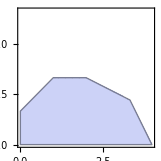

```mathematica
b=RegionPlot[x+2y ≤ 6 && 2x+y ≤8 && -x+y ≤ 1&& y≤ 2 && x≥ 0 && y≥ 0, {x,0,4},{y,0,4}]
```

```mathematica
Show[a,b]
```

```mathematica
Show
```

```mathematica
Manipulación de Matrices
```

```mathematica
M={{}};
H={{}};
n=2;
While[n≤10, For[i=1, i<=n, For[j=1,j<=n, If[i==j,H= Insert[H,2 i, {1,j}]]; If[i<j,H= Insert[H,1,{1,j}]];If[i>j,H= Insert[H,0,{1,j}]];j++]; If[i==1, M=H];If [i!= 1,M=AppendColumns[M,H]];H={{}}; i++];Print[Tr[M]]; n++]
```

```mathematica
M={{}};
H={{}};
n=1;
While[n≤10, For[i=1, i<=n, For[j=1,j<=n, If[i+j==n+1,H= Insert[H,1, {1,j}]]; If[i+j!= n+1,H= Insert[H,0,{1,j}]];j++]; If[i==1, M=H];If [i!= 1,M=AppendColumns[M,H]];H={{}}; i++];Print[Det[M]]; n++]
```

```mathematica
M={{}};
H={{}};
n=2;
While[n≤10, If[Mod[n,2]==0, For[i=1, i<=n, For[j=1,j<=n,If[i== j,H= Insert[H,α,{1,j}]];If[i+j==n+1,H= Insert[H,β, {1,j}]]; If[i+j!= n+1  && i≠j,H= Insert[H,0,{1,j}]]; j++];If[i==1, M=H];If [i!= 1,M=AppendColumns[M,H]];H={{}}; i++];Print[Factor[Det[M]]]]; n++]
```

```mathematica
(* Jordan-Gauss *)
T=({{2, 1, 3, 4, 2, 1, 0, 0, 0, 0}, {1, 2, 3, -1, 4, 0, 1, 0, 0, 0}, {2, 3, 2, 1, 4, 0, 0, 1, 0, 0}, {5, -1, 3, 2, 6, 0, 0, 0, 1, 0}, {3, 1, 0, -5, 2, 0, 0, 0, 0, 1}});
For[j=1,j≤5, For[i=1, i≤5, If[i==j,T[[i]]=1/T[[i,j]]*T[[i]]];If[i≠j, T[[i]]=T[[i]]-T[[i,j]]*1/T[[j,j]]*T[[j]]];Print[MatrixForm[T]]; i++];j++; If [j==6, Print[MatrixForm[T]]]]
```

```mathematica
(* Cofactores *)
T=({{2, 1, 3, 4, 2}, {1, 2, 3, -1, 4}, {2, 3, 2, 1, 4}, {5, -1, 3, 2, 6}, {3, 1, 0, -5, 2}});
NADJ=({{0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}});
M=({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
u=1;
l=1;
For[i=1,i≤5, For[j=1, j≤5,For[h=1, h≤5,For[k=1, k≤5,If [h≠ i && k≠ j,M=ReplacePart[M,T[[h,k]],{u,l}]; If [u≤4,l++]; If[l== 5, u++; l=1]]; k++]; h++];u=1; l=1;NADJ=ReplacePart[NADJ,(-1)^(i+j) Det[M],{i,j}]; j++]; i++; If [i==6, Print[MatrixForm[1/Det[T] Transpose[NADJ]]]]]
```

## Modelos de Programación Lineal

System`DualLinearProgramming

Attributes[DualLinearProgramming]={Protected}
 
Options[DualLinearProgramming]={Method→Automatic,Tolerance→Automatic}